# 绳上的球 ckj 2020-08-25

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
```

目前的问题：
γ 未知，需要实验测
k 的大小影响吗？
μ 多大？
摩擦力（大小、方向）怎么算？两段绳的张力不一样怎么办？
碰撞的处理

参数设置

```mathematica
{g=9.8,m2=0.0133,m3=0.0133,k=1000,γ=0.01,c= 0.001479,μ=.5,l0=1.0(*0.825*),R=0.025};
{x1[t_]=0.1Sin[10t],y1[t_]= 0,z1[t_]=0};
```

列方程

```mathematica
tmax=5;
init=Block[{l1=0.3,l2=0.6,θ1= 30Degree,ϕ1=0 Degree,θ2= 50Degree,ϕ2= 40 Degree,v2vec={0,.5,0},v3vec={-.5,0,0}},
If[l1+l2>l0,Echo["初始长度超啦！"]];
{
{Through[{x2,y2,z2}@0]==l1{Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],-Cos@θ1},Through[{x3,y3,z3}@0]==l1{Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],-Cos@θ1}+l2{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],-Cos@θ2}},
{{x2'[0],y2'[0],z2'[0]}==v2vec,{x3'[0],y3'[0],z3'[0]}==v3vec}
}];

l1[t_]:=√(#.#)&@({x2[t],y2[t],z2[t]}-{x1[t],y1[t],z1[t]})
l2[t_]:=√(#.#)&@({x2[t],y2[t],z2[t]}-{x3[t],y3[t],z3[t]})
l[t_]:=l1[t]+l2[t]
T[t_]:=k Ramp[l[t]-l0]
vec12[t_]:=Through[{x2,y2,z2}[t]]-Through[{x1,y1,z1}[t]](*从 1 指向 2*)
vec23[t_]:=Through[{x3,y3,z3}[t]]-Through[{x2,y2,z2}[t]]


deqns={
m2{x2''[t],y2''[t],z2''[t]}==-c{x2'[t],y2'[t], z2'[t]}+T[t] (-vec12[t])/l1[t]+T[t] vec23[t]/l2[t]+{0,0,-m2 g}+μ Sign[l1'[t]]UnitStep[(l[t]-l0)]Norm@(T[t] (-vec12[t])/l1[t]+T[t] vec23[t]/l2[t]) (-vec12[t])/l1[t] (*摩擦力的方向有点问题*),
m3 {x3''[t],y3''[t], z3''[t]}==-c {x3'[t],y3'[t], z3'[t]}+T[t] (-vec23[t])/l2[t]+γ *l'[t]UnitStep[(l[t]-l0)](-vec23[t])/l2[t]+{0,0,-m3 g}
};

event={WhenEvent[Evaluate[l1[t]≤2R],{"StopIntegration",Echo["l1≤2R"],Echo[tmax=t,"tmax="]}],WhenEvent[Evaluate[l2[t]≤2R],{"StopIntegration",Echo["l2≤2R"],Echo[tmax=t,"tmax="]}]};
```

解方程

```mathematica
tnow=0;
ProgressIndicator[Dynamic@tnow,{0,tmax}]
```

```mathematica
(sol=Flatten@NDSolve[{deqns,init,event},{x2,y2,z2,x3,y3,z3},{t,0,tmax}(*,Method-> {"IndexReduction" ->Automatic}*),EvaluationMonitor:>(tnow=t)])//AbsoluteTiming
```

l2≤2R

tmax=  2.74335

{4.6408,{x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…],z3→InterpolatingFunction[…]}}

画图

```mathematica
Manipulate[
Graphics3D[{{PointSize[.025],{Red,Ball[{x2[t],y2[t],z2[t]},R]},{Blue, Ball[{x3[t],y3[t],z3[t]},R]},If[l[t]>l0,Red,Black],Line[{{x1[t],y1[t],z1[t]},{x2[t],y2[t],z2[t]},{x3[t],y3[t],z3[t]}}]}/. sol,
{Gray,Line[Map[Function[Evaluate[{x3[#],y3[#],z3[#]} /.sol]],Range[0,t,0.01]]]}},PlotRange->{{-1,1},{-1,1},{-1,1}},ImageSize->500],{t,0,tmax}]
```

```mathematica
VectorAngle
```

## 数据处理

```mathematica
Import["/Users/chenkejian/Downloads/QQ 下载/侧面上下m1.xlsx"]
```

{{{质量_A,,},{t,x,y},{0.,-40.1423,22.2064},{0.0042291,-40.0809,23.5347},2395,{9.98731,-50.2817,37.8834},{9.99154,-49.8155,38.8798},{9.99577,-49.5537,40.111},{10.,-49.083,41.1545}}}
 |  |  |  |

```mathematica
%510[[1,3;;]]
```

{{0.,-40.1423,22.2064},{0.0042291,-40.0809,23.5347},{0.00845819,-40.0303,25.0578},{0.0124859,-40.0354,26.5991},2394,{9.99154,-49.8155,38.8798},{9.99577,-49.5537,40.111},{10.,-49.083,41.1545}}
 |  |  |  |

```mathematica
x1func=Interpolation[%515⟦;;,{1,2}⟧]
```

InterpolatingFunction[…]

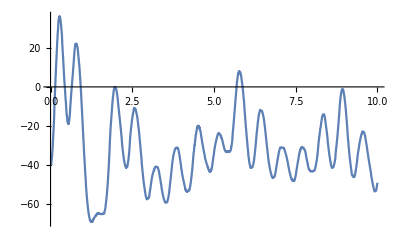

```mathematica
Plot[x1func[t],{t,0,10}]
```

```mathematica
Plot[%519[x],{x,0.,10.}]
```

-Graphics-